```mathematica
ClearAll["Global`*"]
```

# Draw Δ P^1 CR — Δ P^0 L Interpolant

Here we import resulting from cpp unit ../../user.cpp mesh 𝒯 and vectors (u⃗)_1, (u⃗)_2, and p⃗ (for velocity 𝒫(u⃗)_i and 𝒫 p⃗ FE interpolants).
We provide all post–processing routine here.

## Import Mesh 𝒯

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../../Tools/Mathematica/triangulation.nb"]
```

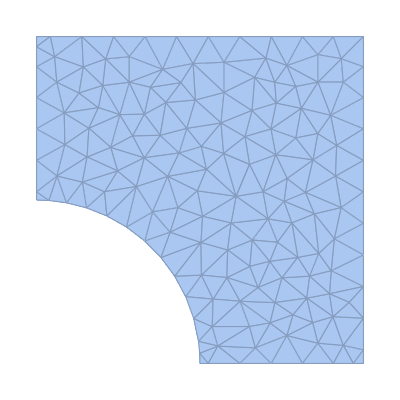

```mathematica
SetDirectory@NotebookDirectory[];
𝒯=importNTR["nodes.dat","triangles.dat","ribs.dat"];
ℛ=region@𝒯
```

## Visualize 𝒯

Our cpp unit ../../user.cpp refined and extended initial mesh generated with ../Generate Mesh/generateMesh.nb from “Nodes and Triangles” to “Nodes, Simple Ribs, and Triangles” format, i.e. it added ribs’ (mid nodes’) numeration which will be used in order to enumerate DOFs of Δ P^1 Crouzeix–Raviart finite elements.

Here we plot resulting mesh 𝒯.

```mathematica
highlight[𝒯,{"nodesNumn","localNodesNumn","trianglesNumn","ribsNumn"}]
```

-Graphics-

## Draw Interpolant

### Shape Functions of Δ P^1 CR Finite Element

```mathematica
shapeFuncsCoef=Inverse@{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]},{1,1,1}};
Subscript[CR, 1][u_,v_]=FullSimplify[shapeFuncsCoef[[1]].{u,v,1}];
Subscript[CR, 2][u_,v_]=FullSimplify[shapeFuncsCoef[[2]].{u,v,1}];
Subscript[CR, 3][u_,v_]=FullSimplify[shapeFuncsCoef[[3]].{u,v,1}];
(* compute shape funcs of t^th triangle of 𝒯 *)
Subscript[S, ΔP1CR][𝒯_,t_]:={Subscript[CR, 1][x,y],Subscript[CR, 2][x,y],Subscript[CR, 3][x,y]}/.Flatten@Table[{Subscript[x, j]->𝓂[𝒯,t][[j,1]],Subscript[y, j]->𝓂[𝒯,t][[j,2]]},{j,3}]
(* get numeration of shape funcs of t^th triangle of 𝒯 *)
Subscript[numnOfS, ΔP1CR][𝒯_,t_]:=𝒯["ribs"][[t]]+1
```

```mathematica
Plot3D[Evaluate@Subscript[S, ΔP1CR][𝒯,1],{x,y}∈Δ[𝒯,1],
AxesLabel->{"x","y","z"},
PlotLegends->{"S_1","S_2","S_3"},
PlotLabel->"Crouzeix–Raviart Shape Funcs",
Mesh->None
]
```

-Graphics3D-

### Shape Function of Δ P^0 L Finite Element

```mathematica
(* compute shape funcs of t^th triangle of 𝒯 *)
Subscript[S, ΔP0L][𝒯_,t_]:={1.}
(* get numeration of shape funcs of t^th triangle of 𝒯 *)
Subscript[numnOfS, ΔP0L][𝒯_,t_]:={t}
```

```mathematica
Plot3D[Subscript[S, ΔP0L][𝒯,1],{x,y}∈Δ[𝒯,1],
AxesLabel->{"x","y","z"},
PlotLegends->{"S_1"},
PlotLabel->"Lagrange P^0 Shape Func",
Mesh->None
]
```

-Graphics3D-

### Set Funcs u =, ⟨u_1,u_2⟩, p Load Vectors (u⃗)_1, (u⃗)_2, and p⃗

```mathematica
u1[x_,y_]:=Sin[4(x^2+y^2)]
u2[x_,y_]:=x+2y
p[x_,y_]:=Norm@{x,y}
```

```mathematica
u1Vec=Import["u1.dat"][[1]];
u2Vec=Import["u2.dat"][[1]];
pVec=Import["p.dat"][[1]];
```

### Draw Δ P^1 CR Interpolants for Velocity components, Δ P^0 L for Pressure

```mathematica
computeInterpolant[basisCoefs_,𝒯_,shapeFuncs_,numnOfShapeFuncs_]:=Module[{ξ,interpolant={}},
Do[
ξ=basisCoefs[[numnOfShapeFuncs[𝒯,t]]];
AppendTo[interpolant,ξ.shapeFuncs[𝒯,t]],
{t,numbOfΔ@𝒯}];
interpolant
]
computePlots[interpolant_,𝒯_]:=Table[Plot3D[interpolant[[t]],{x,y}∈Δ[𝒯,t],Mesh->None,PlotRange->All],{t,numbOfΔ@𝒯}]
```

#### Compute Interpolants and Show Plots

```mathematica
u1Interpolant=computeInterpolant[u1Vec,𝒯,Subscript[S, ΔP1CR],Subscript[numnOfS, ΔP1CR]];
u1Plots=computePlots[u1Interpolant,𝒯];
```

```mathematica
u2Interpolant=computeInterpolant[u2Vec,𝒯,Subscript[S, ΔP1CR],Subscript[numnOfS, ΔP1CR]];
u2Plots=computePlots[u2Interpolant,𝒯];
```

```mathematica
pInterpolant=computeInterpolant[pVec,𝒯,Subscript[S, ΔP0L],Subscript[numnOfS, ΔP0L]];
pPlots=computePlots[pInterpolant,𝒯];
```

```mathematica
Show[
Plot3D[{u1[x,y],0},{x,y}∈ℛ,
PlotLabel->Style["1^st velocity component u_1","Subsubsection"],
PlotRange->All,
Mesh->None,
PlotStyle->{{Blue,Opacity@.5},{Opacity@0}}],
ImageSize->800
]
Show[
Plot3D[0,{x,y}∈ℛ,
PlotLabel->Style["CR–interpolant 𝒫 (u⃗)_1 of the 1^st velocity component u_1","Subsubsection"],
PlotRange->All,
Mesh->None,
PlotStyle->Opacity@0],
u1Plots,
ImageSize->800
]
Show[
Plot3D[0,{x,y}∈ℛ,
PlotLabel->Style["2^nd velocity component u_2 / its Δ P^1 CR–interpolant 𝒫 (u⃗)_2, 𝒫 (u⃗)_2 = u_2 since u_2 is linear","Subsubsection"],
PlotRange->All,
Mesh->None,
PlotStyle->Opacity@0],
u2Plots,
ImageSize->800
]
Show[
Plot3D[p[x,y],{x,y}∈ℛ,
PlotLabel->Style["Pressure distribution p (purple) and its Δ P^0 L–interpolant 𝒫 p","Subsubsection"],
PlotRange->All,
Mesh->None,
PlotStyle->{Purple,Opacity@.5}],
pPlots,
ImageSize->800
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

### Draw Δ P^1 CR — Δ P^0 L Interpolant for ,⟨u, p⟩

```mathematica
computeVelocityPlot[v_,𝒯_]:=Module[{centroids=centroids@𝒯},
ListVectorPlot[Table[{
centroids[[t]],
v[[t]]/.{x->centroids[[t,1]],y->centroids[[t,2]]}
},{t,numbOfΔ@𝒯}],
VectorPoints->centroids,
VectorStyle->Black
]
]
computePressurePlot[p_,𝒯_]:=ListDensityPlot[
Table[Append[centroid[𝒯,t],p[[t]]],{t,numbOfΔ@𝒯}],
ColorFunction->"DeepSeaColors",
PlotLegends->Automatic,
InterpolationOrder->0,
RegionFunction->Function[{x,y},{x,y}∈region@𝒯]
]
```

#### Show Plot

```mathematica
uInterpolant=Table[{u1Interpolant[[t]],u2Interpolant[[t]]},{t,numbOfΔ@𝒯}];
```

```mathematica
velocityPressurePlot={
computePressurePlot[pInterpolant,𝒯],
computeVelocityPlot[uInterpolant,𝒯]
};
```

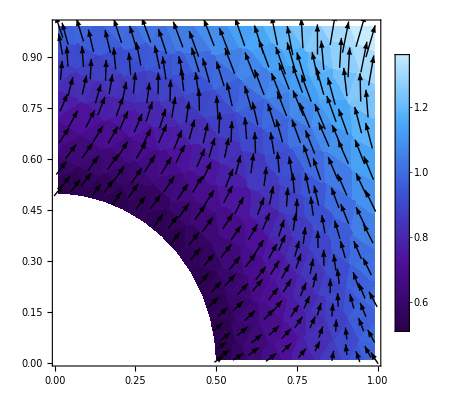

```mathematica
Show[velocityPressurePlot]
```

### Comute errors’ norms||u_i-𝒫(u⃗)_i(||)_(L_2(Ω)) and ||p-𝒫 p⃗(||)_(L_2(Ω))